# Helper funcs

```mathematica
figuresDir="figures_ma/";
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ[figuresDir],CreateDirectory[figuresDir]];
```

```mathematica
plotHist1D[data_,title_]:=Histogram[Flatten[data],ChartStyle->{Directive[Opacity[0.8],Darker[Green]]},ImageSize->400,PlotLabel->title]
```

```mathematica
plotHist2D[data_,title_]:=Grid[{
Table[
plotHist1D[data[[;;,i]],title<>" dim "<>ToString[i]]
,{i,Dimensions[data][[2]]}]
}]
```

```mathematica
getScatterRange[data_]:=Module[
{xMin,xMax,xWidth,yMean,xMean,yMin,yMax,yWidth},
xMin=Min[data[[;;,1]]];
xMax=Max[data[[;;,1]]];
yMin=Min[data[[;;,2]]];
yMax=Max[data[[;;,2]]];

xWidth=xMax-xMin;
yWidth=yMax-yMin;

If[xWidth>yWidth
,
yMean=Mean[data[[;;,2]]];
yMin=yMean-xWidth/2.0;
yMax=yMean+xWidth/2.0;
,
xMean=Mean[data[[;;,1]]];
xMin=xMean-yWidth/2.0;
xMax=xMean+yWidth/2.0;
];

Return[{{xMin,xMax},{yMin,yMax}}]
]
```

```mathematica
plotScatterVisible2D[data_,title_]:=ListPlot[data,PlotStyle->Red,PlotLabel->title,FrameLabel->{"Data dim 1","Data dim 2"},PlotRange->getScatterRange[data]]
```

```mathematica
plotScatterVisibleAndActivated2D[data_,actVisible_]:=Module[
{plt,leg},
plt=Show[
ListPlot[data,PlotStyle->Red,FrameLabel->{"Data dim 1","Data dim 2"}],
ListPlot[actVisible,PlotStyle->Blue],
PlotRange->getScatterRange[data]
];
leg=LineLegend[{Red,Blue},{"Data","Sampled"}];
Return[Grid[{{plt,leg}}]]
]
```

```mathematica
plotDataVisibleAndActivated[data_,actVisible_]:=Module[
{leg,plts,p,dimVis},

dimVis=Dimensions[data][[2]];

leg=LineLegend[{Directive[Opacity[0.5],Red],Directive[Opacity[0.3],Blue]},{"Data","Sampled"}];
plts=Table[
Show[
Histogram[data[[;;,i]],ChartStyle->{Directive[Opacity[0.5],Red]}],
Histogram[actVisible[[;;,i]],ChartStyle->{Directive[Opacity[0.3],Blue]}],
ImageSize->400,
PlotLabel->"Visible dim "<>ToString[i]
]
,{i,dimVis}];
p=Grid[{
Join[plts,{leg}]
}];

Return[p];
]
```

```mathematica
sampleVisibleGivenHidden[weightML_,muML_,varML_,hiddenSamples_]:=Module[
{actVisible,cov,mean,d},

d=Dimensions[weightML][[1]];

actVisible={};
Do[
mean=weightML.dataHidden+muML;
cov=varML*IdentityMatrix[d];
AppendTo[actVisible,RandomVariate[MultinormalDistribution[mean,cov]]];
,{dataHidden,hiddenSamples}];

Return[actVisible];
]
```

```mathematica
sampleHiddenGivenVisible[weightML_,muML_,varML_,visibleSamples_]:=Module[
{actHidden,mean,m,cov,q},

q=Dimensions[weightML][[2]];
m=Transpose[weightML].weightML+varML*IdentityMatrix[q];

cov=varML*Inverse[m];
actHidden={};
Do[
mean=Inverse[m].Transpose[weightML].(dataVisible-muML);
AppendTo[actHidden,RandomVariate[MultinormalDistribution[mean,cov]]];
,{dataVisible,visibleSamples}];

Return[actHidden];
]
```

# Load data

```mathematica
data={{2655,3033},{2744,3012},{2562,2997},{2524,3019},{2742,3007},{2558,3038},{2940,3045},{2714,3005},{2618,3044},{2601,3041},{2845,3004},{2682,3023},{2797,3033},{2528,3000},{2587,3024},{2601,2999},{2620,3018},{2546,3022},{2778,3019},{2870,3030},{2854,3027},{2644,3013},{3041,3016},{2686,3034},{2526,3010},{2732,3019},{2594,3022},{2926,3037},{2478,3026},{2544,3018},{2848,3010},{2450,3012},{2606,3021},{2649,3035},{2783,3025},{2600,3017},{2432,2999},{2544,3025},{2587,3011},{2745,3011},{2709,3039},{2742,3014},{2600,3049},{2913,3015},{2563,3035},{2824,3006},{2747,3024},{2450,3035},{2658,3030},{2536,3012},{2738,3022},{2512,3028},{2646,3026},{2615,3030},{2740,3010},{2448,3032},{2469,3014},{2526,3024},{2639,3010},{2852,3005},{2854,2995},{2807,3023},{2594,3005},{2557,3041},{2535,3035},{2386,3026},{2923,3031},{2851,3048},{2468,3026},{2670,3023},{2512,3005},{2917,3015},{2384,3019},{2750,3043},{2760,2998},{2512,3012},{2824,3023},{2569,3011},{2636,3008},{2852,3015},{2448,3000},{2682,3002},{2705,3026},{2570,2997},{2565,3012},{2657,3021},{2647,3039},{2767,2973},{2869,3034},{2405,3044},{2688,3010},{2511,3009},{2742,3027},{2691,3022},{2686,3009},{2722,3009},{2700,3019},{2965,3016},{2339,3000},{2548,3053},{2985,2997},{2799,3026},{2617,3015},{2669,3033},{2610,3007},{2669,3016},{2926,2997},{2205,3011},{2564,3009},{2592,2999},{2748,3051},{2757,3011},{2579,3035},{2614,3010},{3062,3031},{2679,3008},{2407,3018},{2611,3031},{2895,3037},{2587,3054},{2785,3025},{2690,3010},{2579,3033},{2649,3030},{2507,3001},{2951,3003},{2788,3012},{2538,2967},{2620,3030},{2734,3001},{2528,3041},{2383,3014},{2577,2991},{2752,3008},{2457,3012},{2608,3017},{2635,3024},{2856,3015},{2869,3022},{2519,3031},{3045,3036},{2710,3035},{2568,3025},{2484,3015},{2438,3015},{2707,3025},{2730,3041},{2981,3020},{2544,3018},{2566,3027}};
```

```mathematica
(*
data={{1512,3009},{1510,3008},{1512,3006},{1511,3007},{1513,3017},{1507,3010},{1500,3021},{1510,3016},{1509,3013},{1498,3022},{1504,3011},{1513,3010},{1495,3013},{1516,3008},{1502,3014},{1498,2996},{1509,3010},{1504,3011},{1501,3018},{1502,3014},{1499,3006},{1497,3007},{1508,3008},{1499,3007},{1504,3019},{1510,3014},{1499,3017},{1506,3016},{1511,3010},{1512,3015},{1509,3010},{1502,3002},{1503,3020},{1513,3014},{1511,3008},{1496,3012},{1503,3013},{1513,3015},{1506,3012},{1511,3013},{1503,3013},{1507,3007},{1509,3013},{1506,3012},{1513,3008},{1506,3009},{1499,3014},{1510,3014},{1507,3012},{1502,3014},{1506,3008},{1495,3016},{1510,3013},{1516,3019},{1499,3002},{1507,3017},{1505,3012},{1508,3013},{1511,3009},{1500,3005},{1502,3005},{1505,3014},{1514,3008},{1509,3019},{1518,3009},{1499,3012},{1509,3017},{1506,3016},{1510,3014},{1503,3010},{1498,3007},{1500,3020},{1503,3009},{1518,3018},{1502,3004},{1499,3012},{1502,3018},{1508,3008},{1502,3007},{1505,3012},{1510,3007},{1506,3013},{1506,3017},{1510,3008},{1499,3024},{1503,3009},{1512,3014},{1498,3013},{1502,3015},{1503,3011},{1506,3012},{1505,3005},{1504,3013},{1512,3012},{1509,3011},{1505,3009},{1500,3016},{1513,3013},{1503,3011},{1509,3006},{1503,3011},{1504,3011},{1504,3004},{1502,3008},{1503,3013},{1512,3011},{1514,3009},{1513,3010},{1503,3018},{1504,3014},{1507,3009},{1507,3011},{1507,3019},{1505,3010},{1504,3010},{1503,3012},{1508,3011},{1509,3007},{1507,3016},{1503,3011},{1508,3011},{1502,3001},{1519,3018},{1510,3011},{1508,3014},{1506,3010},{1500,3022},{1497,3007},{1504,3014},{1502,3018},{1509,3003},{1507,3016},{1505,3005},{1505,3007},{1503,3005},{1506,3017},{1510,3012},{1507,3016},{1506,3015},{1504,3016},{1512,3019},{1506,3017},{1508,3007},{1512,3015},{1504,3013},{1502,3011},{1502,3017},{1508,3015},{1506,3005},{1506,3005}};
*)
```

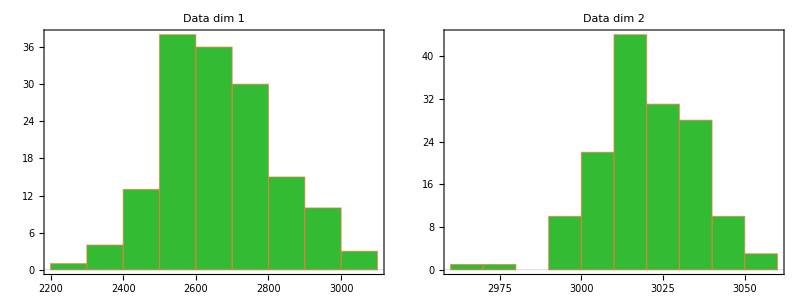

figures_ma/data.png

```mathematica
p=plotHist2D[data,"Data"]
Export[figuresDir<>"data.png",p,ImageResolution->200]
```

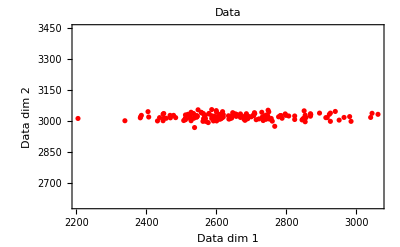

figures_ma/data_scatter.png

```mathematica
p=plotScatterVisible2D[data,"Data"]
Export[figuresDir<>"data_scatter.png",p,ImageResolution->200]
```

# Mean and cov

```mathematica
d=Dimensions[data][[2]];
```

```mathematica
muML=Mean[data]//N;
muML//MatrixForm
```

(2662.33
3019.5)

```mathematica
dataCov=Covariance[data]//N
```

{{24829.,102.742},{102.742,218.01}}

# Weights

## No hidden variables < No visibles = d

```mathematica
q=1;
```

## Variance

```mathematica
{lambdas,eigenvecsT}=Eigensystem[dataCov];
eigenvecs=Transpose[eigenvecsT];
```

```mathematica
varML=(1.0/(d-q))*Sum[lambdas[[j]],{j,q+1,d}]
```

217.581

## Weight matrix

```mathematica
{1,2,3,4}[[;;3]]
```

{1,2,3}

```mathematica
uq=eigenvecs[[;;,;;q]];
uq//MatrixForm
```

(-0.999991
-0.00417452)

```mathematica
lambdaq=DiagonalMatrix[lambdas[[;;q]]];
lambdaq//MatrixForm
```

(24829.4)

```mathematica
weightML=uq.Sqrt[lambdaq-varML*IdentityMatrix[q]];
weightML//MatrixForm
```

(-156.88
-0.654905)

# Sample hidden from visible

```mathematica
actHidden=sampleHiddenGivenVisible[weightML,muML,varML,data];
```

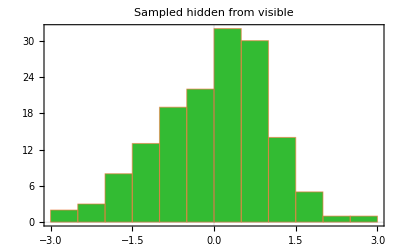

figures_ma/sample_hidden_from_visible.png

```mathematica
p=plotHist1D[actHidden,"Sampled hidden from visible"]
Export[figuresDir<>"sample_hidden_from_visible.png",p,ImageResolution->200]
```

# Sample new visibles

## Sample hidden

```mathematica
noSamples=Length[data];
mean=ConstantArray[0,q];
cov=IdentityMatrix[q];
hiddenSamples=RandomVariate[MultinormalDistribution[mean,cov],noSamples];
```

## Sample visible given hidden

```mathematica
actVisible=sampleVisibleGivenHidden[weightML,muML,varML,hiddenSamples];
```

```mathematica
Print["Covariance visibles (data): ",dataCov//MatrixForm]
Print["Covariance visibles (sampled): ",Covariance[actVisible]//MatrixForm]
```

Covariance visibles (data): (24829. | 102.742
102.742 | 218.01)

Covariance visibles (sampled): (24184.7 | -54.791
-54.791 | 185.505)

```mathematica
Print["Mean visibles (data): ",muML//MatrixForm]
Print["Mean visibles (sampled): ",Mean[actVisible]//MatrixForm]
```

Mean visibles (data): (2662.33
3019.5)

Mean visibles (sampled): (2674.48
3017.14)

## Plot

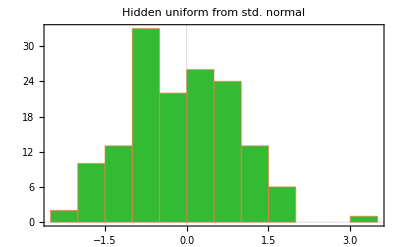

figures_ma/sample_hidden_std_normal.png

```mathematica
p=plotHist1D[hiddenSamples,"Hidden uniform from std. normal"]
Export[figuresDir<>"sample_hidden_std_normal.png",p,ImageResolution->200]
```

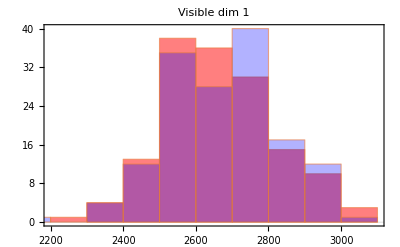
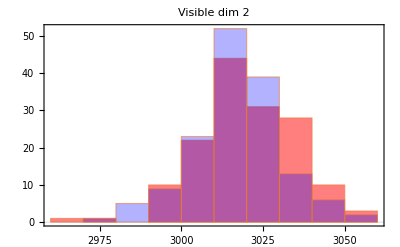
-Graphics- | -Graphics- |

figures_ma/sample_visible_from_hidden.png

```mathematica
p=plotDataVisibleAndActivated[data,actVisible]
Export[figuresDir<>"sample_visible_from_hidden.png",p,ImageResolution->200]
```

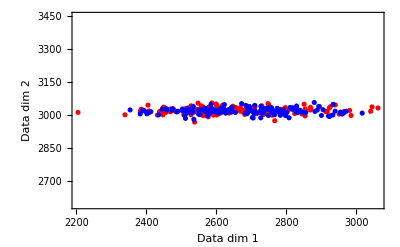
-Graphics- |

figures_ma/sample_visible_from_hidden.png

```mathematica
p=plotScatterVisibleAndActivated2D[data,actVisible]
Export[figuresDir<>"sample_visible_from_hidden.png",p,ImageResolution->200]
```

# Rescale to arbitrary latent variable Gaussian

## Rescale

```mathematica
meanHidden={120.0};
covHidden={{23.0}};
weightMLRescaled=weightML.MatrixPower[covHidden,-0.5];
muMLRescaled=muML-weightMLRescaled.meanHidden;
muMLRescaled//MatrixForm
weightMLRescaled//MatrixForm
```

(6587.74
3035.89)

(-32.7118
-0.136557)

## Sample hidden

```mathematica
noSamples=Length[data];
hiddenSamples=RandomVariate[MultinormalDistribution[meanHidden,covHidden],noSamples];
```

## Sample visible from hidden

```mathematica
actVisible=sampleVisibleGivenHidden[weightMLRescaled,muMLRescaled,varML,hiddenSamples];
```

```mathematica
Print["Covariance visibles (data): ",dataCov//MatrixForm]
Print["Covariance visibles (sampled): ",Covariance[actVisible]//MatrixForm]
```

Covariance visibles (data): (24829. | 102.742
102.742 | 218.01)

Covariance visibles (sampled): (25847.1 | 390.165
390.165 | 281.38)

```mathematica
Print["Mean visibles (data): ",muML//MatrixForm]
Print["Mean visibles (sampled): ",Mean[actVisible]//MatrixForm]
```

Mean visibles (data): (2662.33
3019.5)

Mean visibles (sampled): (2657.31
3018.96)

## Plot

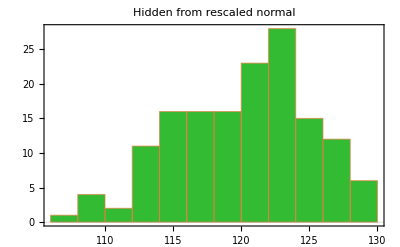

figures_ma/sample_hidden_from_rescaled_normal.png

```mathematica
p=plotHist1D[hiddenSamples,"Hidden from rescaled normal"]
Export[figuresDir<>"sample_hidden_from_rescaled_normal.png",p,ImageResolution->200]
```

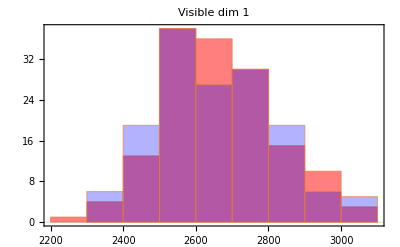
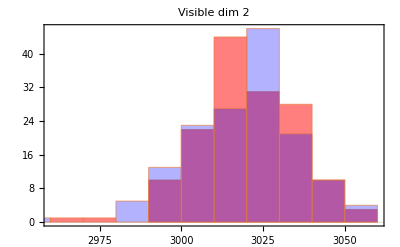
-Graphics- | -Graphics- |

figures_ma/rescaled_sample_visible_from_hidden.png

```mathematica
p=plotDataVisibleAndActivated[data,actVisible]
Export[figuresDir<>"rescaled_sample_visible_from_hidden.png",p,ImageResolution->200]
```

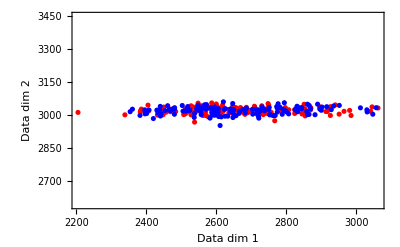
-Graphics- |

figures_ma/rescaled_sample_visible_from_hidden_scatter.png

```mathematica
p=plotScatterVisibleAndActivated2D[data,actVisible]
Export[figuresDir<>"rescaled_sample_visible_from_hidden_scatter.png",p,ImageResolution->200]
```